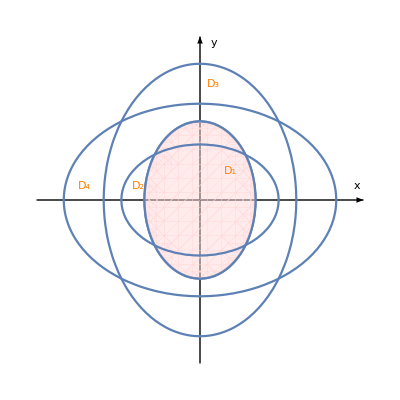

```mathematica
f7=Graphics[{
{Arrowheads[0.03],Arrow[{{-1.2,0},{1.2,0}}]},
{Arrowheads[0.03],Arrow[{{0,-1.2},{0,1.2}}]}
}];
f1=ContourPlot[6x^2+3y^2==1,{x,-1,1},{y,-1,1},Axes->False,Frame->False];
f2=ContourPlot[3x^2+6y^2==1,{x,-1,1},{y,-1,1}];
f3=ContourPlot[2x^2+y^2==1,{x,-1,1},{y,-1,1}];
f4=ContourPlot[x^2+2y^2==1,{x,-1,1},{y,-1,1}];
f5=RegionPlot[6x^2+3y^2<1,{x,-1,1},{y,-1,1},PlotStyle->{LightRed,Opacity[0.5]},Axes->False];
f6=Graphics[
{
Text[Style["D_1",Large,Orange,Italic],{0.22,0.21}],
Text[Style["D_2",Large,Orange,Italic],{-0.45,0.1}],
Text[Style["D_3",Large,Orange,Italic],{0.1,0.85}],
Text[Style["D_4",Large,Orange,Italic],{-0.85,0.1}],
Text[Style["x",Medium,Italic],{1.15,0.1}],
Text[Style["y",Medium,Italic],{0.1,1.15}]
}
];
Show[f7,f1,f5,f2,f3,f4,f6]
```

```mathematica
RegionPlot[6x^2+3y^2<1,{x,-1,1},{y,-1,1},PlotStyle->LightRed,Axes->False]
```